## Chapter 8 Programming

### Section 8.2

Simply append //Head to each of the expressions and enter them, to get:

Rule

Power

List

Function

Simply append //FullForm to each of the expressions and enter them, to get:

Rule[x, 2]

Rational[1, 2]

Power[2,Rational[1,2]]

List[1,2,3]

The head is Derivative[1][a]. Note that FullForm needs to be applied to the Head output in order to reveal this.

```mathematica
Clear[a,x];
a'[x]//FullForm
```

Derivative[1][a][x]

```mathematica
Head[a'[x]]//FullForm
```

Derivative[1][a]

Defer must be applied to this expression to prevent its evaluation. Its FullForm is shown in the output below.

```mathematica
Defer[FullForm[2x+1/.x->3]]
```

ReplaceAll[Plus[Times[2,x],1],Rule[x,3]]

Defer must be applied to this expression to prevent its evaluation. Its FullForm is shown in the output below. In essence, we find that ; is the infix form of the command CompoundExpression.

```mathematica
Defer[FullForm[x=3;2x]]
```

CompoundExpression[Set[x,3],Times[2,x]]

As in the previous exercise, Defer is needed to prevent evaluation.

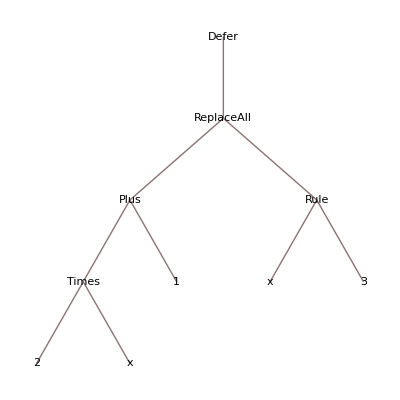

```mathematica
TreeForm[Defer[2x+1/.x->3]]
```

Be sure to Clear any values associated with a, b, c, and d before applying TreeForm.

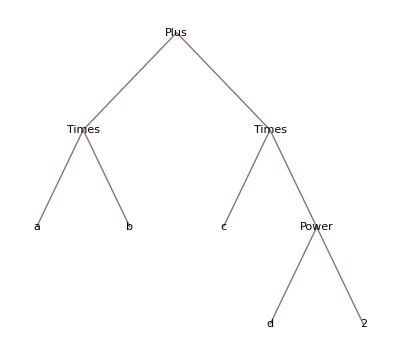

```mathematica
Clear[a,b,c,d];
a*b+c*d^2//TreeForm
```

Here are the basic parts of the expression. Note that the zeroth part is the Head.

```mathematica
(a*b+c*d^2)⟦0⟧//FullForm
```

Plus

```mathematica
(a*b+c*d^2)⟦1⟧//FullForm
```

Times[a,b]

```mathematica
(a*b+c*d^2)⟦2⟧//FullForm
```

Times[c,Power[d,2]]

Here are the sub-parts of the second part:

```mathematica
(a*b+c*d^2)⟦2,1⟧
```

c

```mathematica
(a*b+c*d^2)⟦2,2⟧//FullForm
```

Power[d,2]

Here are the sub-parts of (a*b+c*d^2)⟦2,2⟧:

```mathematica
(a*b+c*d^2)⟦2,2,0⟧
```

Power

```mathematica
(a*b+c*d^2)⟦2,2,1⟧
```

d

```mathematica
(a*b+c*d^2)⟦2,2,2⟧
```

2

The real numbers in the lower left portion of the output will be different when you try it; these represent the coordinates of the tip and tail of the arrow.

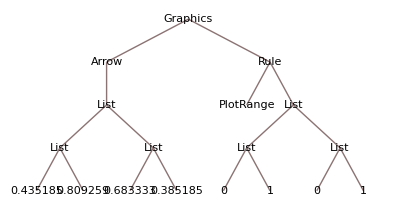

```mathematica
-Graphics-//TreeForm
```

A string is displayed without the double quotations. The FullForm of a string will show the double quotations.

```mathematica
"Here is a string."
```

Here is a string.

```mathematica
"Here is a string."//FullForm
```

"Here is a string."

The strings are concatenated. Note that the first character of the second string is a space character.

```mathematica
"I am"~~" putting strings together."//FullForm
```

"I am putting strings together."

This simply illustrates that ~~ is indeed the infix form of the StringExpression command.

```mathematica
Defer[FullForm["a"~~"b"]]
```

StringExpression["a","b"]

The command below will do the trick. Note the space after the first double quotation.

```mathematica
fav[n_]:=ToString[n]~~" is my favorite number."
```

```mathematica
{fav[467],fav[-17]}//Column
```

467 is my favorite number.
-17 is my favorite number.

```mathematica
Clear[fav]
```

You’ll have to try this on your own.

At the time of this writing there were 327 options for Cell.

```mathematica
Length[Options[Cell]]
```

327

### Section 8.3

The King probably owes more rice than he has in his entire kingdom!

```mathematica
Text@Grid[Prepend[Table[{n,NumberForm[2^(n-1),DigitBlock->3]},{n,1,31}],{"day","grains of rice"}],Alignment->Right,Dividers->Gray]
```

day | grains of rice
1 | 1
2 | 2
3 | 4
4 | 8
5 | 16
6 | 32
7 | 64
8 | 128
9 | 256
10 | 512
11 | 1,024
12 | 2,048
13 | 4,096
14 | 8,192
15 | 16,384
16 | 32,768
17 | 65,536
18 | 131,072
19 | 262,144
20 | 524,288
21 | 1,048,576
22 | 2,097,152
23 | 4,194,304
24 | 8,388,608
25 | 16,777,216
26 | 33,554,432
27 | 67,108,864
28 | 134,217,728
29 | 268,435,456
30 | 536,870,912
31 | 1,073,741,824

The input below shows how to align numbers at the decimal point:

```mathematica
Column[Table[10^n*N[π,6],{n,0,5}],Alignment->".",Dividers->Gray]
```

3.14159
31.4159
314.159
3141.59
31415.9
314159.

### Section 8.4

First is being applied to Rule.

```mathematica
Options[NSolve]
```

{WorkingPrecision→Automatic,Sort→True,MonomialOrder→Automatic,Method→Automatic}

```mathematica
WorkingPrecision->Automatic//FullForm
```

Rule[WorkingPrecision,Automatic]

```mathematica
First/@Options[NSolve]
```

{WorkingPrecision,Sort,MonomialOrder,Method}

The CharacterRange command is the ticket. It produces a list of the characters that start and end with those given as its arguments. Part is then used to extract the desired character.

```mathematica
f=CharacterRange["a","z"]⟦#⟧&
```

CharacterRange[a,z]⟦#1⟧&

```mathematica
f[19]
```

s

The output below shows the FullForm expression.

```mathematica
#^2&//FullForm
```

Function[Power[Slot[1],2]]

The output below shows the FullForm expression.

```mathematica
Norm[{#1,#2}]<3&//FullForm
```

Function[Less[Norm[List[Slot[1],Slot[2]]],3]]

The definition is straightforward:

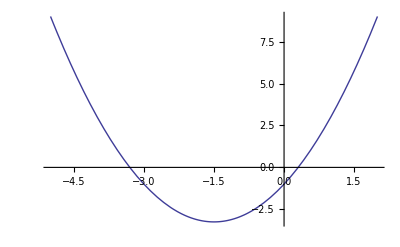

```mathematica
Clear[f];
f=Function[x,x^2+3x-1];
Plot[f[x],{x,-5,2}]
```

Again, the function f defined this way behaves exactly as you would expect:

```mathematica
f'[x]
```

3+2 x

```mathematica
∫f[x]ⅆx
```

-x+(3 x^2)/2+x^3/3

The first argument to Function is a list of the argument names.

```mathematica
Clear[f];
f=Function[{x,y},x^2 y-x+3y]
```

Function[{x,y},x^2 y-x+3 y]

Recall that vector fields in Mathematica are given as lists of coordinate functions. So the second argument to Function is also a list in this case.

```mathematica
Clear[f];
f=Function[{x,y},{x^2 y-x+3y,Cos[x]}]
```

Function[{x,y},{x^2 y-x+3 y,Cos[x]}]

Each row of the table is of the form List[lhs, rhs]. We could use Apply[Equal, #]& on each row to replace the head List with Equal. That is, we Map this pure function over t, and then display the result. Equivalently, we could supply a third argument to Apply to specify the level in the table at which Equal is applied. In this case, we apply it at level 1.

```mathematica
Clear[t,k,a];
t=Table[{Tan[k a],Together[TrigExpand[Tan[k a]]]},{k,2,9}];
Column[Apply[Equal,t,1],Dividers->Gray]//TraditionalForm
```

tan(2 a)==(2 cos(a) sin(a))/(cos^2(a)-sin^2(a))
tan(3 a)==(sec(a) (3 cos^2(a) sin(a)-sin^3(a)))/(cos^2(a)-3 sin^2(a))
tan(4 a)==(4 (cos^3(a) sin(a)-cos(a) sin^3(a)))/(cos^4(a)-6 sin^2(a) cos^2(a)+sin^4(a))
tan(5 a)==(sec(a) (sin^5(a)-10 cos^2(a) sin^3(a)+5 cos^4(a) sin(a)))/(cos^4(a)-10 sin^2(a) cos^2(a)+5 sin^4(a))
tan(6 a)==(2 (3 sin(a) cos^5(a)-10 sin^3(a) cos^3(a)+3 sin^5(a) cos(a)))/(cos^6(a)-15 sin^2(a) cos^4(a)+15 sin^4(a) cos^2(a)-sin^6(a))
tan(7 a)==(sec(a) (-sin^7(a)+21 cos^2(a) sin^5(a)-35 cos^4(a) sin^3(a)+7 cos^6(a) sin(a)))/(cos^6(a)-21 sin^2(a) cos^4(a)+35 sin^4(a) cos^2(a)-7 sin^6(a))
tan(8 a)==(8 (sin(a) cos^7(a)-7 sin^3(a) cos^5(a)+7 sin^5(a) cos^3(a)-sin^7(a) cos(a)))/(cos^8(a)-28 sin^2(a) cos^6(a)+70 sin^4(a) cos^4(a)-28 sin^6(a) cos^2(a)+sin^8(a))
tan(9 a)==(sec(a) (sin^9(a)-36 cos^2(a) sin^7(a)+126 cos^4(a) sin^5(a)-84 cos^6(a) sin^3(a)+9 cos^8(a) sin(a)))/(cos^8(a)-36 sin^2(a) cos^6(a)+126 sin^4(a) cos^4(a)-84 sin^6(a) cos^2(a)+9 sin^8(a))

Each row of the table is of the form List[lhs, rhs]. Use Apply[Rule, #]& on each row to replace the head List with Rule. That is, we Map this pure function over t, and then display the result with TabView. Again, we utilize the third argument to Apply to specify that it is to applied at level 1. In the second input below, we finesse this idea in order to specify the display style of both the tabs and the content pane.

```mathematica
TabView[Apply[Rule,t,1]]//TraditionalForm
```

12345678

```mathematica
TabView@Apply[Rule[Style[TraditionalForm[#1],FontFamily->"Times"],Style[TraditionalForm[#2],FontFamily->"Times"]]&,t,1]
```

12345678

```mathematica
Clear[t]
```

You’re on your own with this one.

Here are examples of the constituent commands:

```mathematica
StringReplace["four score and seven years ago",{"a"->"1","s"->"2"}]
```

four 2core 1nd 2even ye1r2 1go

```mathematica
Thread[{"a","s"}->{"1","2"}]
```

{a→1,s→2}

```mathematica
CharacterRange["a","z"]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
RotateLeft[%]
```

{b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,a}

Putting them together we get:

```mathematica
encode[str_]:=StringReplace[str,Thread[CharacterRange["a","z"]->RotateLeft[CharacterRange["a","z"]]]]
```

Using RotateRight to counteract the RotateLeft, we get:

```mathematica
decode[str_]:=StringReplace[str,Thread[CharacterRange["a","z"]->RotateRight[CharacterRange["a","z"]]]]
```

```mathematica
encode["four score and seven years ago"]
```

gpvs tdpsf boe tfwfo zfbst bhp

```mathematica
decode[%]
```

four score and seven years ago

Use the optional second argument to RotateLeft and RotateRight to specify the number of places in the shift.

```mathematica
encode[str_,k_]:=StringReplace[str,Thread[CharacterRange["a","z"]->RotateLeft[CharacterRange["a","z"],k]]]
```

```mathematica
decode[str_,k_]:=StringReplace[str,Thread[CharacterRange["a","z"]->RotateRight[CharacterRange["a","z"],k]]]
```

```mathematica
encode["one small step for a man. one giant leap for mankind.",5]
```

tsj xrfqq xyju ktw f rfs. tsj lnfsy qjfu ktw rfspnsi.

```mathematica
decode[%,5]
```

one small step for a man. one giant leap for mankind.

```mathematica
Clear[encode,decode]
```

### Section 8.5

The input ?*Q will generate an interactive listing of all symbols ending in capital Q. Click on any one to get a usage message. Alternately, the input below will create a simple list of the same commands. There are more than 180 of them!

```mathematica
Names["*Q"]
```

{AcyclicGraphQ,AlgebraicIntegerQ,AlgebraicUnitQ,AntihermitianMatrixQ,AntisymmetricMatrixQ,ArgumentCountQ,ArrayQ,AskedQ,AssociationQ,AtomQ,AudioQ,BinaryImageQ,BipartiteGraphQ,BondQ,BooleanQ,BoundaryMeshRegionQ,BoundedRegionQ,BusinessDayQ,ByteArrayQ,ColorQ,CompatibleUnitQ,CompleteGraphQ,CompositeQ,ConnectedGraphQ,ConnectedMoleculeQ,ConstantRegionQ,ContinuousTimeModelQ,ControllableModelQ,ConvexPolygonQ,ConvexPolyhedronQ,CoprimeQ,DateObjectQ,DateOverlapsQ,DateWithinQ,DaylightQ,DayMatchQ,DeviceOpenQ,DiagonalizableMatrixQ,DiagonalMatrixQ,DictionaryWordQ,DigitQ,DirectedGraphQ,DirectoryQ,DiscreteTimeModelQ,DisjointQ,DispatchQ,DistributionParameterQ,DuplicateFreeQ,EdgeCoverQ,EdgeQ,EdgeWeightedGraphQ,EllipticNomeQ,EmptyGraphQ,EulerianGraphQ,EvenQ,ExactNumberQ,FailureQ,FileExistsQ,FreeQ,GeoWithinQ,GraphQ,GroupElementQ,HamiltonianGraphQ,HermitianMatrixQ,HypergeometricPFQ,ImageContainsQ,ImageInstanceQ,ImageQ,IndefiniteMatrixQ,IndependentEdgeSetQ,IndependentVertexSetQ,InexactNumberQ,IntegerQ,IntersectingQ,IntervalMemberQ,InverseEllipticNomeQ,IrreduciblePolynomialQ,IsomorphicGraphQ,KEdgeConnectedGraphQ,KeyExistsQ,KeyFreeQ,KeyMemberQ,KnownUnitQ,KVertexConnectedGraphQ,LeapYearQ,LegendreQ,LetterQ,LinkConnectedQ,LinkReadyQ,ListQ,LoopFreeGraphQ,LowerCaseQ,LowerTriangularMatrixQ,MachineNumberQ,ManagedLibraryExpressionQ,MandelbrotSetMemberQ,MarcumQ,MatchLocalNameQ,MatchQ,MatrixQ,MemberQ,MersennePrimeExponentQ,MeshRegionQ,MissingQ,MixedGraphQ,MoleculeContainsQ,MoleculeEquivalentQ,MoleculeQ,MultigraphQ,NameQ,NegativeDefiniteMatrixQ,NegativeSemidefiniteMatrixQ,NormalMatrixQ,NumberQ,NumericArrayQ,NumericQ,ObservableModelQ,OddQ,OptionQ,OrderedQ,OrthogonalMatrixQ,OutputControllableModelQ,PacletNewerQ,PalindromeQ,PartitionsQ,PathGraphQ,PerfectNumberQ,PermissionsGroupMemberQ,PermutationCyclesQ,PermutationListQ,PlanarGraphQ,PolynomialQ,PositiveDefiniteMatrixQ,PositiveSemidefiniteMatrixQ,PossibleZeroQ,PrimePowerQ,PrimeQ,PrimitivePolynomialQ,PrintableASCIIQ,ProcessParameterQ,QHypergeometricPFQ,QuadraticIrrationalQ,QuantityQ,QuantityVariableQ,RegionQ,RegularlySampledQ,RootOfUnityQ,SameQ,SatisfiableQ,ScheduledTaskActiveQ,SimpleGraphQ,SimplePolygonQ,SimplePolyhedronQ,SocketReadyQ,SolidRegionQ,SquareFreeQ,SquareMatrixQ,StringContainsQ,StringEndsQ,StringFreeQ,StringMatchQ,StringQ,StringStartsQ,SubsetQ,SymmetricMatrixQ,SyntaxQ,TautologyQ,TensorQ,TetGenExpressionQ,TetGenIntersectingFacetsQ,TimeObjectQ,TreeGraphQ,TrueQ,UnateQ,UndirectedGraphQ,UnitaryMatrixQ,UnsameQ,UpperCaseQ,UpperTriangularMatrixQ,URLAbsoluteQ,URLShortenedQ,ValueQ,VectorQ,VertexCoverQ,VertexQ,VertexWeightedGraphQ,WeaklyConnectedGraphQ,WeightedGraphQ}

```mathematica
Length[%]
```

188

Either of the commands FactorInteger or PrimeQ can be used. We see that the number 2^(2^k)+1 is prime for k=0 through 4, but when k=5, we see that 2^(2^5)+1=2^32+1=641×6700417, and so is a composite number. If you try this for k=8, expect to wait a while, as this is a 78 digit number. However, PrimeQ can handle k=8 and beyond, first showing noticeable signs of slowing (on my laptop) when k=13.

```mathematica
Table[FactorInteger[2^(2^k)+1],{k,0,7}]//Column
```

{{3,1}}
{{5,1}}
{{17,1}}
{{257,1}}
{{65537,1}}
{{641,1},{6700417,1}}
{{274177,1},{67280421310721,1}}
{{59649589127497217,1},{5704689200685129054721,1}}

```mathematica
2^(2^8)//N
```

1.15792×10^77

```mathematica
Table[PrimeQ[2^(2^k)+1],{k,0,13}]
```

{True,True,True,True,True,False,False,False,False,False,False,False,False,False}

Increment will add one to its argument and return the old value of the argument, and PreIncrement will add one to its argument and return the new value of the argument. In fact, ++k has the same effect as the assignment k=k+1. In the last output below, we see that both variables hold the same value after one iteration.

```mathematica
j=1;j++
```

1

```mathematica
k=1;++k
```

2

```mathematica
{j,k}
```

{2,2}

```mathematica
Clear[j,k]
```

The While loop suggests that the answer is n=54. The calculation below confirms that this value of n meets the criteria, and the ListPlot shows the overall trend, confirming that this is indeed the first value of n with the desired property.

```mathematica
n=1;
While[Integrate[x^n,{x,0,21/20-1/n}]≤1/10,n++];
n
```

54

```mathematica
NIntegrate[x^54,{x,0,21/20-1/54}]
```

0.100004

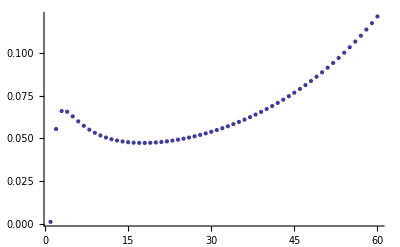

```mathematica
Clear[n];
ListPlot@Table[NIntegrate[x^n,{x,0,21/20-1/n}],{n,60}]
```

Either of the inputs below does the trick. Note that the results will be different each time it is executed. Note also that the increment and body (third and fourth arguments to For) are swapped in the two inputs below. This illustrates a general point: the sequence of evaluation at each step in a For loop is test, body, increment. So in the first input, the initial value 1 is not printed, while in the second input, the final (prime) value is not printed.

```mathematica
For[k=1,!PrimeQ[k],Print[k],k=k+RandomInteger[{1,100}]]
```

76

93

164

253

301

305

377

382

388

420

462

488

502

602

605

640

645

744

841

879

957

974

1012

1045

1090

1097

```mathematica
For[k=1,!PrimeQ[k],k=k+RandomInteger[{1,100}],Print[k]]
```

1

58

158

209

297

368

407

```mathematica
k
```

479

Here is one way to proceed. We use the command AppendTo, which appends the next value to the end of the list ls, then resets ls to be the appended list. The For loop only has three arguments here.

```mathematica
For[ls={1},!PrimeQ[Last[ls]],AppendTo[ls,Last[ls]+RandomInteger[{1,100}]]];ls
```

{1,38,39,57,113}

Just change the last part from ls to Length[ls]-1.

```mathematica
For[ls={1},!PrimeQ[Last[ls]],AppendTo[ls,Last[ls]+RandomInteger[{1,100}]]];Length[ls]-1
```

2

In the first input we encode the procedure from part c. We use SetDelayed (:=) so that the loop evaluates anew each time doIt is called (see the second input). The command Tally will count the occurrences of each item in a list and return a list of two-tuples. The first item in each two-tuple is a member of the original list, and the second item is the number of times that item appeared in the original list. The final output below displays the tally. It shows a single iteration was the most common outcome (about a quarter of the time, or in roughly 250 out of 1000 trials), but that in rare cases dozens of iterations were required.

```mathematica
doIt:=(For[ls={1},!PrimeQ[Last[ls]],AppendTo[ls,Last[ls]+RandomInteger[{1,100}]]];Length[ls]-1)
```

```mathematica
Table[doIt,{10}]
```

{4,4,3,2,1,15,1,6,10,8}

```mathematica
Tally[%]
```

{{4,2},{3,1},{2,1},{1,2},{15,1},{6,1},{10,1},{8,1}}

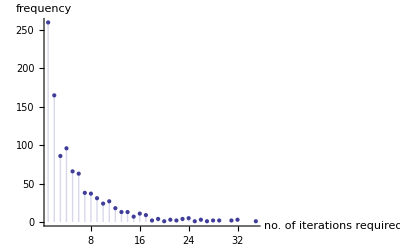

```mathematica
ListPlot[Tally@Table[doIt,{1000}],Filling->Axis,PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"no. of iterations required","frequency"}]
```

```mathematica
Clear[ls,doIt]
```

### Section 8.6

The dummy variable s represents the partial sum. We keep it in a Module to insulate it from any assignments that may have been made to that symbol. The For loop keeps resetting s to be its previous value plus 1/i, for i ranging from 1 to n. The final value of s is reported. Note there is a built-in command HarmonicNumber that produces the same output.

```mathematica
harmonicNumber[n_]:=Module[{s=0},For[i=1,i≤n,i++,s=s+1/i];s]
```

```mathematica
harmonicNumber[100]
```

14466636279520351160221518043104131447711/2788815009188499086581352357412492142272

```mathematica
HarmonicNumber[100]
```

14466636279520351160221518043104131447711/2788815009188499086581352357412492142272

```mathematica
Clear[harmonicNumber]
```

Here is what happens:

```mathematica
Do[Module[{x},Print[x]],{10}]
```

x$5710

x$5711

x$5712

x$5713

x$5714

x$5715

x$5716

x$5717

x$5718

x$5719

The output is exactly what you would expect.

```mathematica
x=3;Block[{x=2},Print[x]];x
```

2

3

This is subtle. The assignment on the first line gives an expression expr in terms of x. When the Block is executed, x has been temporarily changed to 2, so the quantity x + expr evaluates to 2+2+1=5. When Module is evaluated, only the x in the body is localized (to something like x$30041), while expr still utilizes the symbol x that exists outside the Module.

```mathematica
Clear[x];expr=x+1
```

1+x

```mathematica
Block[{x=2},x+expr]
```

5

```mathematica
Module[{x=2},x+expr]
```

3+x

```mathematica
Clear[expr]
```

### Section 8.7

Function[x,  10x]

```mathematica
Nest[Function[x,10x],x,4]
```

10000 x

Function[x,x^2]

```mathematica
Nest[Function[x,x^2],x,4]
```

x^16

Function[x,√(1+x)]

```mathematica
Nest[Function[x,√(1+x)],x,4]
```

√(1+√(1+√(1+√(1+x))))

Function[x,1/(1 + x)]

```mathematica
Nest[Function[x,1/(1+x)],x,4]
```

1/(1+1/(1+1/(1+1/(1+x))))

NestWhileList will produce a list of ten thousand numbers, many of them very large, so we use NestWhile instead in order to produce only the last number in this list. If a palindrome is produced anywhere along the way it will be returned. Rather than print the output (a number with over 4000 digits), we inspect it programmatically. Note that the Print command will cause a message to be printed even when it is followed by a semicolon. This is useful when you wish to report several distinct facts, as we do here.

```mathematica
bigNumber=NestWhile[#+FromDigits[Reverse[IntegerDigits[#]]]&, 196, IntegerDigits[#] ≠ Reverse[IntegerDigits[#]] &, 1, 10000];
Print["The final number has " ~~ToString[Length[id=IntegerDigits[bigNumber]]] ~~" digits."];
If[id==Reverse[id],"It's a palindrome.","It's not a palindrome."]
```

The final number has 4159 digits.

It's not a palindrome.

```mathematica
Clear[bigNumber,id]
```

Below is another version of the procedure shown above, but this one uses the commands PalindromeQ and IntegerReverse (introduced in version 10 of Mathematica), which makes the coding slightly simpler:

```mathematica
bigNumber=NestWhile[#+IntegerReverse[#]&, 196, !PalindromeQ[#]&, 1,10000];
Print["The final number has " ~~ToString[Length[id=IntegerDigits[bigNumber]]] ~~" digits."];
If[PalindromeQ[bigNumber],"It's a palindrome.","It's not a palindrome."]
```

```mathematica
Clear[bigNumber,id]
```

We represent the iterated function f(x)=1/x+x/2 as a pure function.

```mathematica
NestList[1/#+#/2&,N[1,20],10]
```

{1.,1.5,1.4166666666666666667,1.414215686274509804,1.414213562374689911,1.414213562373095049,1.414213562373095049,1.414213562373095049,1.414213562373095049,1.414213562373095049,1.414213562373095049}

The command RealDigits produces two items (in a list). The first is a list of the digits appearing in the real number, and the second is the number of these digits appearing to the left of the decimal point. For instance RealDigits[100] will produce the output {{1, 0, 0}, 3}. In this case, we simply want the First part of the output—the list of digits.

```mathematica
First[RealDigits[#]] & /@%
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,4,1,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6},{1,4,1,4,2,1,5,6,8,6,2,7,4,5,0,9,8,0,3,9},{1,4,1,4,2,1,3,5,6,2,3,7,4,6,8,9,9,1,0,6},{1,4,1,4,2,1,3,5,6,2,3,7,3,0,9,5,0,4,8,8},{1,4,1,4,2,1,3,5,6,2,3,7,3,0,9,5,0,4,8,8},{1,4,1,4,2,1,3,5,6,2,3,7,3,0,9,5,0,4,8,8},{1,4,1,4,2,1,3,5,6,2,3,7,3,0,9,5,0,4,8,8},{1,4,1,4,2,1,3,5,6,2,3,7,3,0,9,5,0,4,8,8},{1,4,1,4,2,1,3,5,6,2,3,7,3,0,9,5,0,4,8,8}}

ArrayPlot will represent each digit by a different gray-tone (0 is white, 9 is black).

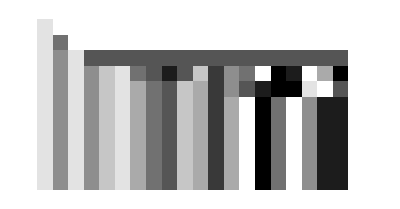

```mathematica
ArrayPlot[%]
```

It is clear that 100 digit precision is obtained in fewer than 10 iterations, as all columns become “stable” by the last few iterates.

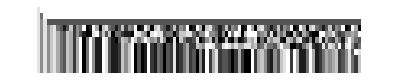

```mathematica
ArrayPlot[First[RealDigits[#]]&/@NestList[1/#+#/2&,N[1,100],10]]
```

In this case it takes more than 200 iterations to obtain stability in all 100 digits. This iteration converges to a fixed point, but convergence occurs far more slowly. The (approximate) straight line running diagonally across the image is indicative of what is called “linear convergence.” In the previous part, we are looking at the “quadratic convergence” typical of the Newton-Raphson method. In fact, the function 1/#+#/2& being iterated is the result of applying the Newton-Raphson technique to find a root of 2-x^2=0.

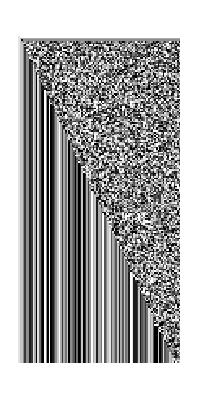

```mathematica
ArrayPlot[First[RealDigits[#]]&/@NestList[1/#+#/3&,N[1,100],200]]
```

You will force ArrayPlot to use the Rainbow color gradient. Any named color gradient will work.

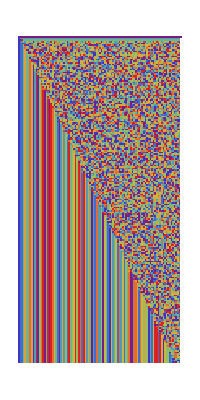

```mathematica
ArrayPlot[First[RealDigits[#]]&/@NestList[1/#+#/3&,N[1,100],200],ColorFunction->"Rainbow"]
```

There are many ways to proceed, but here’s an efficient method, broken down step by step. The points in the list (x_0,x_0), (x_0,f(x_0)), (f(x_0),f(x_0)), (f(x_0),f(f(x_0))) will be produced in pairs. In the first input below, we use the optional third argument to Map to specify that f should only be applied at the second level to the list of two points. The result is a list of the next two points. The same procedure can be applied to this output to produce the next two points, and so on. In the third input, we use NestList to iterate this process, and in the fourth input we apply Flatten at level 1 to strip the extra brackets (grouping pairs of two-tuples). The last input shows the final result, where this list of points is wrapped in Line in the Epilog of the Plot. This image shows 50 iterations.

```mathematica
Clear[f,x0];
Map[f,{{x0,x0},{x0,f[x0]}},{2}]
```

{{f[x0],f[x0]},{f[x0],f[f[x0]]}}

```mathematica
Map[f,%,{2}]
```

{{f[f[x0]],f[f[x0]]},{f[f[x0]],f[f[f[x0]]]}}

```mathematica
NestList[Map[f,#,{2}]&,{{x0,x0},{x0,f[x0]}},2]
```

{{{x0,x0},{x0,f[x0]}},{{f[x0],f[x0]},{f[x0],f[f[x0]]}},{{f[f[x0]],f[f[x0]]},{f[f[x0]],f[f[f[x0]]]}}}

```mathematica
Flatten[%,1]
```

{{x0,x0},{x0,f[x0]},{f[x0],f[x0]},{f[x0],f[f[x0]]},{f[f[x0]],f[f[x0]]},{f[f[x0]],f[f[f[x0]]]}}

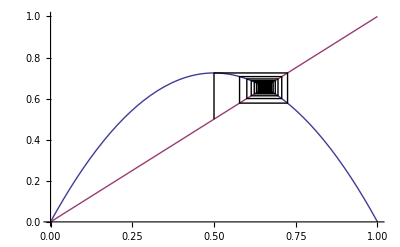

```mathematica
With[{f=Function[x,2.9x(1-x)],x0=.5},Plot[{f[x],x},{x,0,1},Epilog->Line[
Flatten[NestList[Map[f,#,{2}]&,{{x0,x0},{x0,f[x0]}},50],1]]]]
```

The code works by iterating a (somewhat complex but very elegantly defined) pure function that accepts a pair {x_(n-1), x_n} of numbers, and returns the next pair {x_n,x_(n+1)}. We demonstrate on f(x)=x^3-2x+2 with just three iterations. We then give a forty digit approximation of the final value after nine iterations. This agrees precisely with the example from the text that used a Do loop (with 38 of the 40 digits being correct). You will notice in a live session that Mathematica’s automatic syntax coloring does not particularly like this command, as it will color the x in the first argument to Function red in the right side of the definition for secantMethodList. Despite the warning, this poses no problem.

```mathematica
secantMethodList[f_,{x_,x0_,x1_},n_]:=NestList[Last[#]-{0,(Function[x,f][Last[#]]*Subtract@@#)/Subtract@@Function[x,f]/@#}&,{x0,x1},n]
```

```mathematica
secantMethodList[x^3-2x+2,{x,-1,-3/2},3]
```

{{-1,-3/2},{-3/2,-23/11},{-23/11,-6419/3755},{-6419/3755,-26587376488/15130484341}}

```mathematica
N[secantMethodList[x^3-2x+2,{x,-1,-3/2},9]⟦-1,-1⟧,40]
```

-1.769292354238631415240409464335033492634

```mathematica
Clear[secantMethodList]
```

All the hard work was in the previous exercise. The Manipulate is straightforward. The example below includes a PlotLabel that accounts for about a third of the code. For small values of a we see a convergent sequence, but as a increases the iterates sometimes find stable orbits, and other times diverge into chaos. This one is very fun to play with in a live session.

```mathematica
Manipulate[With[{f=Function[x,a x(1-x)]},Plot[{f[x],x},{x,0,1},Epilog->Line[
Flatten[NestList[Map[f,#,{2}]&,{{x0,x0},{x0,f[x0]}},100],1]],PlotLabel->"100 iterates of f(x) = " ~~ToString[a] ~~" x(1-x) starting at x_0= " ~~ToString[x0]]],
{{a,3.63},2.5,3.7},{{x0,.1,"x_0"},.01,.99}]
```

If you are not familiar with continued fractions, take a moment and read about them at MathWorld.

This is a routine evaluation:

```mathematica
ContinuedFraction[10/7]
```

{1,2,3}

```mathematica
1+1/(2+1/3)
```

10/7

Here is one way to do this. Essentially, the digit list must be reversed (read from right to left). The command Last tears off the last member of the digit list (equivalently, the first member of the reversed digit list), and the command Rest produces the rest of that list. In a live session, you can enter the outputs shown below and evaluate them.

```mathematica
displayCF[digitList_]:=Fold[Defer[#2+1/#1]&,Last[digitList],Rest[Reverse[digitList]]]
```

```mathematica
displayCF[{1,2,3}]
```

1+1/(2+1/3)

```mathematica
ContinuedFraction[4/123]
```

{0,30,1,3}

```mathematica
displayCF[%]
```

0+1/(30+1/(1+1/3))

Here is a finite continued fraction that is very close to π:

```mathematica
displayCF@ContinuedFraction[Rationalize[π,10^-20]]
```

3+1/(7+1/(15+1/(1+1/(292+1/(1+1/(1+1/(1+1/(2+1/(1+1/(3+1/(1+1/(14+1/(2+1/(1+1/(1+1/(2+1/(2+1/(2+1/3))))))))))))))))))

```mathematica
Clear[displayCF]
```

The plot shows that the convergence is very slow; even after 1000 iterations only a few decimal places of accuracy are obtained. This is one reason why it was such a difficult problem—it was simply not tenable to make an educated guess for the limit of the series on the basis of calculations of partial sums (especially back in the early eighteenth century)!

```mathematica
Accumulate[Table[1/n^2,{n,10}]]
```

{1,5/4,49/36,205/144,5269/3600,5369/3600,266681/176400,1077749/705600,9778141/6350400,1968329/1270080}

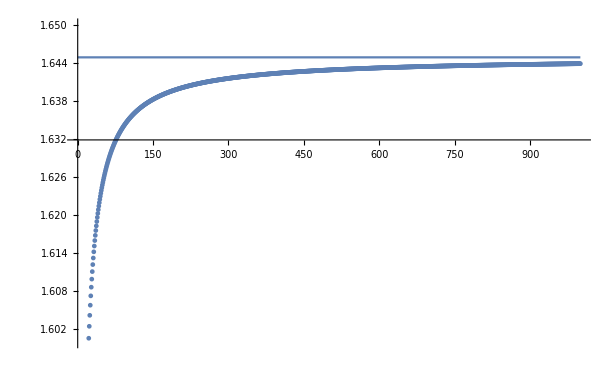

```mathematica
Show[ListPlot@Accumulate[Table[1./n^2,{n,1000}]],Plot[π^2/6,{x,0,1000}],PlotRange->{1.6,1.65}]
```

### Section 8.8

Recall that the predicate command EvenQ will return True only if its argument is an even integer.

The command And (&&) can be used to construct a pure predicate function.

```mathematica
Clear[f];
f[x_?(EvenQ[#]&&#>10&)]:="success"
```

The command Or (||) can be used to construct a pure predicate function.

```mathematica
Clear[f];
f[x_?(EvenQ[#]||#>10&)]:="success"
```

No, the expression x_1 is Pattern[x,Blank[]] multiplied by the number 1, which evaluates to Pattern[x, Blank[]]. It will match any expression. If you wish to define a function f that will only accept the input 1, simply type f[1] = followed by your definition.

Quadrangles fits the bill. Triple underscores are used in the input below since it may be that there are no intermediate letters in one or both portions represented by the triple underscores. Indeed, this is the case for the second one.

```mathematica
DictionaryLookup["q"~~___~~"angle"~~___~~"s"]
```

{quadrangles}

Here is a simple implementation, with a randomly produced example.

```mathematica
complementaryDNA[seq_List]:=seq/.{"A"->"T","T"->"A","C"->"G","G"->"C"}
```

```mathematica
Grid[{s=RandomChoice[{"A","C","G","T"},20],complementaryDNA[s]}]
```

C | A | T | G | A | C | A | A | A | T | G | G | C | A | T | G | A | A | C | T
G | T | A | C | T | G | T | T | T | A | C | C | G | T | A | C | T | T | G | A

```mathematica
Clear[s,complementaryDNA]
```

This is straightforward, based on the example given in the text.

```mathematica
Clear[f,collatz];
f[n_?EvenQ]:=n/2;
f[n_?OddQ]:=3n+1;
collatz[n_]:=NestWhileList[f,n,#≠1&,1,1000]
```

No more than 20 or so iterations were needed, so we are certain that every orbit ends in 1. That is, we have not found here a counterexample to the Collatz conjecture.

```mathematica
data=Table[collatz[n],{n,20}];
```

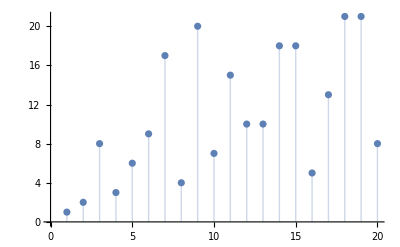

```mathematica
ListPlot[Length/@data,Filling->Axis,AxesOrigin->{0,0},PlotRange->All]
```

The second argument to Partition is 2 (to get a partition into pairs). The third argument is 1 (to specify an offset of 1).

```mathematica
Partition[#, 2, 1] & /@ data
```

{{},{{2,1}},{{3,10},{10,5},{5,16},{16,8},{8,4},{4,2},{2,1}},{{4,2},{2,1}},{{5,16},{16,8},{8,4},{4,2},{2,1}},{{6,3},{3,10},{10,5},{5,16},{16,8},{8,4},{4,2},{2,1}},{{7,22},{22,11},{11,34},{34,17},{17,52},{52,26},{26,13},{13,40},{40,20},{20,10},{10,5},{5,16},{16,8},{8,4},{4,2},{2,1}},{{8,4},{4,2},{2,1}},{{9,28},{28,14},{14,7},{7,22},{22,11},{11,34},{34,17},{17,52},{52,26},{26,13},{13,40},{40,20},{20,10},{10,5},{5,16},{16,8},{8,4},{4,2},{2,1}},{{10,5},{5,16},{16,8},{8,4},{4,2},{2,1}},{{11,34},{34,17},{17,52},{52,26},{26,13},{13,40},{40,20},{20,10},{10,5},{5,16},{16,8},{8,4},{4,2},{2,1}},{{12,6},{6,3},{3,10},{10,5},{5,16},{16,8},{8,4},{4,2},{2,1}},{{13,40},{40,20},{20,10},{10,5},{5,16},{16,8},{8,4},{4,2},{2,1}},{{14,7},{7,22},{22,11},{11,34},{34,17},{17,52},{52,26},{26,13},{13,40},{40,20},{20,10},{10,5},{5,16},{16,8},{8,4},{4,2},{2,1}},{{15,46},{46,23},{23,70},{70,35},{35,106},{106,53},{53,160},{160,80},{80,40},{40,20},{20,10},{10,5},{5,16},{16,8},{8,4},{4,2},{2,1}},{{16,8},{8,4},{4,2},{2,1}},{{17,52},{52,26},{26,13},{13,40},{40,20},{20,10},{10,5},{5,16},{16,8},{8,4},{4,2},{2,1}},{{18,9},{9,28},{28,14},{14,7},{7,22},{22,11},{11,34},{34,17},{17,52},{52,26},{26,13},{13,40},{40,20},{20,10},{10,5},{5,16},{16,8},{8,4},{4,2},{2,1}},{{19,58},{58,29},{29,88},{88,44},{44,22},{22,11},{11,34},{34,17},{17,52},{52,26},{26,13},{13,40},{40,20},{20,10},{10,5},{5,16},{16,8},{8,4},{4,2},{2,1}},{{20,10},{10,5},{5,16},{16,8},{8,4},{4,2},{2,1}}}

Flatten the result at level 1 to produce a single list of pairs, then feed that list of pairs to the Union command (to eliminate duplicate pairs).

```mathematica
Union@Flatten[Partition[#, 2, 1] & /@ data,1]
```

{{2,1},{3,10},{4,2},{5,16},{6,3},{7,22},{8,4},{9,28},{10,5},{11,34},{12,6},{13,40},{14,7},{15,46},{16,8},{17,52},{18,9},{19,58},{20,10},{22,11},{23,70},{26,13},{28,14},{29,88},{34,17},{35,106},{40,20},{44,22},{46,23},{52,26},{53,160},{58,29},{70,35},{80,40},{88,44},{106,53},{160,80}}

Use Map to Apply the command Rule to each pair from part c to obtain an amalgamated list of all orbits. It should end like this: {…,88 → 44,106 → 53,160 → 80}. Now display the result as a directed Graph to get a visualization of the orbit space for the Collatz process.

```mathematica
rules=Map[Apply[Rule,#]&,%]
```

{2→1,3→10,4→2,5→16,6→3,7→22,8→4,9→28,10→5,11→34,12→6,13→40,14→7,15→46,16→8,17→52,18→9,19→58,20→10,22→11,23→70,26→13,28→14,29→88,34→17,35→106,40→20,44→22,46→23,52→26,53→160,58→29,70→35,80→40,88→44,106→53,160→80}

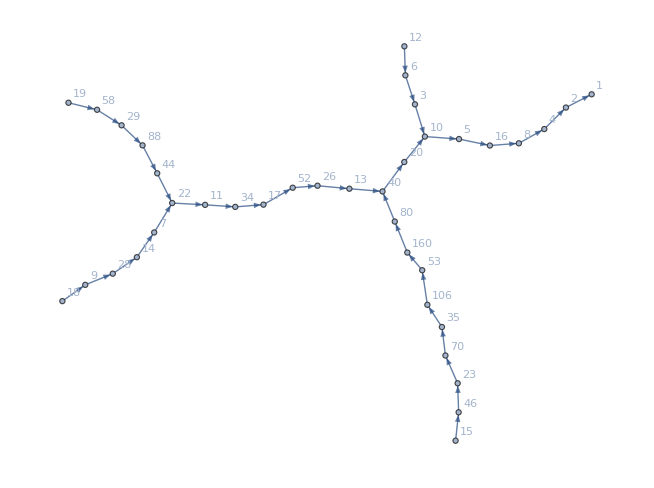

```mathematica
Graph[rules,VertexLabels->Automatic,GraphLayout->"SpringEmbedding"]
```

Here it is for 100 integers. The process for 1000 is similar. Unfortunately, it is not easy to find the branch that ends in 1 with these images until the image is enlarged greatly. (It happens to be a twig on the upper-right branch.) The Documentation Center has information on the various layouts available to Graph. Each will produce a slightly different embedding, and a particular graph may look better using one method over another. In this case, the important point is that the graph is a tree (it has a single connected component, and no cycles). If the Collatz conjecture were false, there would be more than one component in a sufficiently large graph of this type.

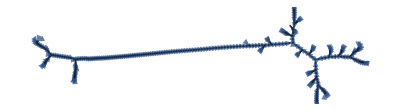

```mathematica
data=Table[collatz[n],{n,100}];
Graph[Map[Apply[Rule,#]&,Union@Flatten[Partition[#, 2, 1] & /@ data,1]],GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
Clear[f,collatz,data,rules]
```

Setting a=π/(3k), the argument to the function cos(k a) is π/3, so the function evaluates to 1/2. This can be used to construct polynomials with a root of the form cos(π/(3k)) by using the expressions on the right in the table. Sometimes these factor, yielding even simpler polynomials. For this exercise we proceed with k=7, and a=π/(3k)=π/21. The first input below verifies that the expression on the right side of the table evaluates to 1/2. Subtract 1/2 from this polynomial, and multiply by 2 to clear fractions, and we see that cos(π/21) is a root of this polynomial. Finally, factor the polynomial. One factor has a root at 1/2. So the other factor must have one of its roots at cos(π/21).

```mathematica
64 x^7-112 x^5+56 x^3-7x/.x->Cos[π/21]//FullSimplify
```

1/2

```mathematica
128 x^7-224 x^5+112 x^3-14x-1/.x->Cos[π/21]//FullSimplify
```

0

```mathematica
Factor[128 x^7-224 x^5+112 x^3-14x-1]
```

(-1+2 x) (1+16 x+32 x^2-48 x^3-96 x^4+32 x^5+64 x^6)

Replace opts___Rule with opts:OptionsPattern[].

```mathematica
Clear[myPlot];
myPlot[f_,iter_List,opts:OptionsPattern[]]:=Plot[f,iter,opts,PlotStyle->Thick,PlotLabel->"y = "~~ToString[TraditionalForm[f]],AxesLabel->{iter⟦1⟧,"y"}]
```

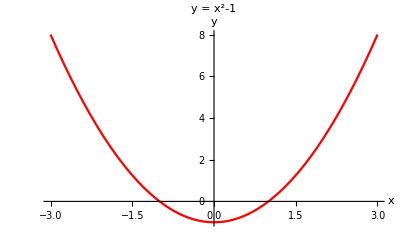

```mathematica
myPlot[x^2-1,{x,-3,3},PlotStyle->Red]
```

```mathematica
Clear[myPlot]
```

TabView requires a list of rules, where the left side of each rule is the tab label, while the right side is the value to be displayed when that tab is clicked. So the right side of the require replacement rule is itself a rule!

```mathematica
Range[15]/.n_Integer->(Defer[n!]->n!)
```

{1!→1,2!→2,3!→6,4!→24,5!→120,6!→720,7!→5040,8!→40320,9!→362880,10!→3628800,11!→39916800,12!→479001600,13!→6227020800,14!→87178291200,15!→1307674368000}

```mathematica
TabView[%,13]
```

123456789101112131415

The Split command will split a list into runs of identical elements, as illustrated by the first input below. The replacement in the right side of the definition for scaleRuns takes and list of ones (the pattern a:{1..}) and replaces it with its product with the scalar Length[a] .  RuleDelayed (:> or :>) is used to make this replacement, so that the expression Length[a] * a is not evaluated until after the replacement has been made (otherwise the undefined symbol a has length zero, as illustrated in the third output below).

```mathematica
Split[{1,1,1,1,0,1,1,0,1,1,1,0,0,1,1,1}]
```

{{1,1,1,1},{0},{1,1},{0},{1,1,1},{0,0},{1,1,1}}

```mathematica
{1,1,1,1}/.a:{1..}:>Length[a]*a
```

{4,4,4,4}

```mathematica
{1,1,1,1}/.a:{1..}->Length[a]*a
```

0

```mathematica
scaleRuns[ℒ_]:=Flatten[Split[ℒ]/.a:{1..}:>Length[a]*a]
```

```mathematica
scaleRuns[{1,1,1,1,0,1,1,0,1,1,1,0,0,1,1,1}]
```

{4,4,4,4,0,2,2,0,3,3,3,0,0,3,3,3}

This is straightforward. Note that ArrayPlot requires a list of lists, so the argument in the first definition below includes a set of curly brackets around scaleRuns. The final output has in interesting interpretation: imagine a basketball player who is a 50% free-throw shooter. If she were to take 1000 free-throws over the course of a season, one would expect a run of ten or more consecutive baskets somewhere along the line (dark bands in the output can be thought of as runs of consecutive baskets). This happens even in a model that never gets a “hot hand.” In other words, if an actual human player is declared uncharacteristically hot or cold on a given night, it could be that she is being treated unfairly. Runs are to be expected, even in a completely random setting such as this where hot and cold have no meaning. The likelihood of hot streaks increases even further for a player who is better than a 50% shooter.

```mathematica
showRuns[ℒ_]:=ArrayPlot[{scaleRuns[ℒ]}]
```

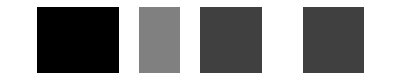

```mathematica
showRuns[{1,1,1,1,0,1,1,0,1,1,1,0,0,1,1,1}]
```

```mathematica
showRuns[ℒ_?(Length[#]>50&)]:=ArrayPlot[scaleRuns/@Partition[ℒ,50]]
```

```mathematica
showRuns[Table[RandomInteger[],{1000}]]
```

-Graphics-

```mathematica
Clear[scaleRuns,showRuns]
```

Here is the definition and an example. The :3 on the second argument gives that argument the default value of 3 if the user omits it (this is the ItemSize option to Grid). The nth differences for a list of evenly spaced inputs to an nth degree polynomial will be constant. Here, for instance, we see the third differences for this particular cubic (evaluated on the first twelve positive integers) will all be 6. All subsequent differences must therefore be zero.

```mathematica
differenceTable[ls_List,itemSize_:3]:=Column[Table[Grid[{Differences[ls,k]},ItemSize->itemSize],{k,0,Length[ls]-1}],Alignment->Center]
```

```mathematica
differenceTable[(#^3+3#^2-2#+3&)/@Range[12]]
```

5 | 19 | 51 | 107 | 193 | 315 | 479 | 691 | 957 | 1283 | 1675 | 2139
14 | 32 | 56 | 86 | 122 | 164 | 212 | 266 | 326 | 392 | 464
18 | 24 | 30 | 36 | 42 | 48 | 54 | 60 | 66 | 72
6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0
0 | 0
0

```mathematica
Clear[differenceTable]
```